```mathematica
NS["whykantorovich"]
```

```mathematica
setdirectory;
```

```mathematica
bins={0.5,40.5,1};
```

```mathematica
data0=Flatten[{Table[{1,3},50],Table[2,100]}];
data1=Flatten[{Table[{6,8},50],Table[7,100]}];
data2=Flatten[{Table[{38,40},50],Table[39,100]}];
```

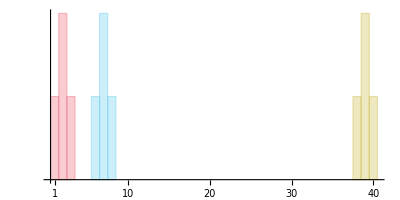

```mathematica
myfontsize=6;Histogram[{data0,data1,data2},bins,"PDF",Axes->{True,False},PlotRange->All,ChartBaseStyle->Opacity[0.33],ChartStyle->{Directive[red],Directive[EdgeForm[Dashed],blue],Directive[EdgeForm[Dotted],yellow]},Ticks->{Join[{1},Range[10,40,10],Table[{i,""},{i,40}]]},AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}]
```

```mathematica
expdf0["whykantorovich"]
```

whykantorovich.pdf

```mathematica
{p0,p1,p2}=(HistogramList[#,bins,"PDF"][[2]]&)/@{data0,data1,data2};
```

```mathematica
p0
```

{0.25,0.5,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ClearAll[kd];kd[p1_,p2_]:=Total[Abs[Accumulate[p1-p2]]]
```

```mathematica
ClearAll[js];js[p1_,p2_]:=Block[{log},log[x_,y_]:=If[x==0 ,0,Log[x/y]];SetAttributes[log,Listable];Total[p1*log[p1,(p1+p2)/2]+p2*log[p2,(p1+p2)/2]]/2]
```

```mathematica
{kd[p0,p1],js[p0,p1]}
```

{5.,0.693147}

```mathematica
{kd[p0,p2],js[p0,p2]}
```

{37.,0.693147}